# MATH 263 Numerical differential equations

Ethan Smith

## Lecture 6: Predictor-corrector methods 11 MAR 2021

## Assigned reading for next time.

Zill, Section 8.1.

## Method implementations.

Disclaimer: The implementations below are not efficient in Mathematica, but they have been chosen for pedagogical reasons.

```mathematica
euler[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n]},
{x[0],y[0]} =N[ {a,y0}];
Do[
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*f[x[i],y[i]];,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

```mathematica
heun[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],k1,k2,w1=0.5,w2=0.5},
{x[0],y[0]} = N[{a,y0}];
Do[
k1=f[x[i],y[i]];
k2=f[x[i]+h,y[i]+h*k1];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(w1*k1 + w2*k2);,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

```mathematica
rk4[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n], k1, k2, k3, k4, w1=1./6, w2=1./3, w3=1./3,w4=1./6},
{x[0],y[0]} = N[{a,y0}];
Do[
k1=f[x[i],y[i]];
k2=f[x[i]+0.5*h,y[i]+0.5*h*k1];
k3=f[x[i]+0.5*h,y[i]+0.5*h*k2];
k4=f[x[i]+h,y[i]+h*k3];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(w1*k1+w2*k2+w3*k3+w4*k4);,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

```mathematica
ab2[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],f1,f2},
{{x[0],y[0]},{x[1],y[1]}}=heun[f,a,a+h,y0,1];
f1=f[x[0],y[0]];
Do[
f1=f[x[i],y[i]];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(3*f1-f2)/2;
(*Shift f evals down to get ready for next step.  Could be done without actually moving the data, but not worth the effort here.*)
f2=f1;,
{i,1,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

```mathematica
abm2[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],yhat,f0,f1,f2},
{{x[0],y[0]},{x[1],y[1]}}=heun[f,a,a+h,y0,1];
f2=f[x[0],y[0]];
Do[
f1=f[x[i],y[i]];
x[i+1]=x[i]+h;
yhat=y[i]+h*(3*f1-f2)/2; (*predict*)
f0=f[x[i+1],yhat];
y[i+1]=y[i]+h*(f0+f1)/2; (*correct*)
(*Shift f evals down to get ready for next step.  Could be done without actually moving the data, but not worth the effort here.*)
f2=f1;,
{i,1,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

## Implicit and predictor-corrector methods.

The numerical methods for solving ODE’s that we have considered so far have all been explicit, which is to say that the formula defining the (i+1)st approximation  can be explicitly solved for y_(i+1) .  Implicit methods are characterized by formula which are not able to solved in the general case.  Suppose for example that we are trying to numerically solve the first order IVP

y’ = f(x,y), y(x_0)=y_0.

Linearization at the ith mesh point x_i and projecting forward along the tangent line yields the (forward) Euler method

y_(i+1) = y_i + h f(x_i,y_i)

which we have already discussed in detail.  On the other hand, linearization at the (i+1)st mesh point x_(i+1) and projecting backward along the tangent line yields the (backward) Euler method

y_(i+1) = y_i + h f(x_(i+1),y_(i+1)).

Since the precise form of the “right-hand side” f(x,y) is not known in advance, we cannot explicitly solve this equation for y_(i+1) in the general case – that is without knowing f(x,y).  If the function f(x,y) turns out to be linear in y, then equation (1) can easily be solved for y.  However, there are many important application where f(x,y) is nonlinear in y.   Thus, in order to use an implicit formula such as (1), it is necessary to incorporate some nonlinear equation solver such as Newton’s method or fixed-point iteration to solve for y_(i+1).  

Since fixed-point iteration techniques require an “initial-guess,” it is common to use an explicit method to “predict” the value of y_(i+1) before employing the implicit method to “correct” the guess.  Thus, the pairing of an explicit predictor method with an implicit corrector method is often referred to as a predictor-corrector method.  The question of how many times to apply the fixed-point iteration of the corrector method can be a delicate matter.  Each iteration brings us closer to the true solution to (1) but at the cost of more evaluations of the function f(x,y).  In theory, one might choose to iterate the corrector until the value y_(i+1) converges to within some tolerance.  Since iteration of (1) only brings us closer to the solution of (1) and not necessarily the true solution y(x_(i+1)), it is often not worth the additional cost to apply more than 1 iteration.  If higher accuracy is needed, it is probably more efficient to reduce the step size h.

### Advantages and disadvantages.

The main advantage of a predictor-corrector method is that the implicit (corrector) method tends to give the method better stability properties.  A numerical method is said to be stable if small perturbations in the initial data do not cause the resulting numerical solution to diverge away from the original as x→ ∞.  The obvious disadvantage of a predictor-corrector method is that each iteration the implicit method costs additional functional evaluations which translates to more work.  To mitigate this effect, the number of corrector iterations per step is generally kept low.

### Adams–Moulton 1-step (implicit) method.

As usual, consider the first order IVP

y’ = f(x,y), y(x_0)=y_0.

Choosing a model of the form

y_(i+1) = α_1 y_i + h (β_0 y'_(i+1)+ β_1 y'_i),

where y_i'=f(x_i,y_i) for each i≥0, we proceed by the method of underdetermined coefficients.  In particular, we force the model to be exact for the first three monomials  y(x)=1, y(x)=x, and y(x)=x^2.  Thus, by a calculation that is precisely similar to the derivation that we gave for the Adams–Bashforth two-step (explicit) method, we ultimately arrive at the formula

y_(i+1)=y_i + h/2(y'_(i+1)+ y'_i)

which defines the Adams–Moulton one-step (implicit) method.  As with the Adams–Bashforth two-step method, the local truncation error is O(h^3) and hence it is considered to be an order 2 method.

This method is often paired with the order 2 Adams–Bashforth two-step (explicit) method to create the order 2 Adams–Bashforth–Moulton (predictor-corrector) method (ABM2)

OverHat[y_(i+1)]=y_i+h/2(3 y'_i-y'_(i-1)),
y_(i+1)=y_i + h/2(OverHat[y_(i+1)]'+ y'_i),

where y_i'=f(x_i,y_i) and OverHat[y_(i+1)'] =f(x_(i+1),OverHat[y_(i+1)]) for each i≥0.  Here, OverHat[y_(i+1)] is referred the predicted value and y_(i+1) the corrected value.

### Adams–Moulton 3-step (implicit) method.

In a similar manner, one may derive the Adams–Moulton three-step (implicit) method, which is defined by the formula

y_(i+1)=y_i+h/24(9 y'_(i+1)+19 y'_i-5 y'_(i-1)+y'_(i-2))

and has local truncation error that is O(h^5).  It is, therefore, considered an order 4 method.

This method is commonly paired with the order 4 Adams–Bashforth four-step (explicit) method to create the order 4 Adams–Bashforth–Moulton (predictor-corrector) method (ABM4)

OverHat[y_(i+1)]=y_i+h/24(55y_i'-59y_(i-1)'+37y_(i-2)'-9y_(i-3)'),
y_(i+1)=y_i+h/24(9OverHat[y_(i+1)]'+19y_i'-5y_(i-1)'+y_(i-2)'),

where y_i'=f(x_i,y_i) and OverHat[y_(i+1)'] =f(x_(i+1),OverHat[y_(i+1)]) for each i≥0.

## Example.

Consider the IVP y'=y-x^2+1, y(0)=1/2.

```mathematica
f[x_,y_]=y-x^2+1;
{x0,y0}={0,1/2};
Y[x_]=y[x]/.DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x][[1]];
StringForm["The exact solution to the IVP is ``.",TraditionalForm[y[x]==Y[x]]]
```

The exact solution to the IVP is y(x)==1/2 (2 x^2+4 x-ⅇ^x+2).

Compare the Adams–Bashforth 2-step method (AB2) and the Adams–Bashforth–Moulton 2-step method (ABM2) with n=10 steps over the interval [a,b]=[0,2].

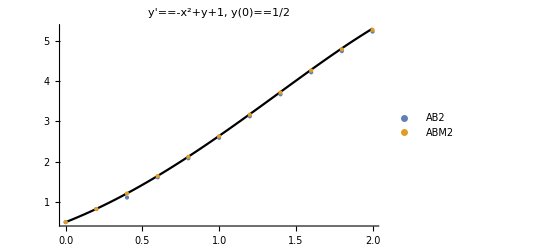

i | ABM2 | AB2
0 | 0. | 0.
1 | 0.00329862 | 0.00329862
2 | 0.00430765 | 0.102732
3 | 0.0055712 | 0.0373806
4 | 0.00718297 | 0.0425215
5 | 0.00923551 | 0.0478947
6 | 0.011845 | 0.0535586
7 | 0.0151575 | 0.0593987
8 | 0.0193565 | 0.0652203
9 | 0.0246721 | 0.0707339
10 | 0.0313931 | 0.0755232|y(x_i)-y_i|

```mathematica
n=10;
{a,b}={0,2};

(*Compute numerical solutions.*)
ab2Soln=ab2[f,a,b,y0,n];
abm2Soln=abm2[f,a,b,y0,n];

(*Compare by plot.*)
Show[
Plot[Y[x],{x,a,b},PlotStyle->Black],
ListPlot[{ab2Soln,abm2Soln},PlotStyle->PointSize[Large],PlotLegends->{"AB2","ABM2"}],
PlotRange->All,
PlotLabel->StringForm["``, ``",TraditionalForm[y'==f[x,y]],TraditionalForm[y[x0]==y0]]
]

(*Compare errors at each step with table.*)
h=N[(b-a)/n];
exactSoln=Table[Y[a+h*i],{i,0,n}];
abm2Soln=abm2Soln[[;;,2]];
abm2Errors=Abs[abm2Soln-exactSoln];
ab2Soln=ab2Soln[[;;,2]];
ab2Errors=Abs[ab2Soln-exactSoln];
Labeled[TableForm[Table[{i-1,abm2Errors[[i]],ab2Errors[[i]]},{i,1,n+1}],TableHeadings->{None,{"i","ABM2","AB2"}}],"|y(x_i)-y_i|",Top]
```

Use both AB2 and ABM2 to approximate y(2) with n=10^j steps for j=1,...,6.  Compare the absolute errors and the time to compute each result.

```mathematica
numSteps=Table[10^j,{j,1,6}];

(*Compute absolute errors and display in table.*)
ynABM2 = Table[Last[abm2[f,a,b,y0,n]][[2]],{n,numSteps}];
ynAB2 = Table[Last[ab2[f,a,b,y0,n]][[2]],{n,numSteps}];
abm2Errors=Abs[ynABM2-Y[b]];
ab2Errors=Abs[ynAB2-Y[b]];
Labeled[TableForm[Transpose[Join[{numSteps,abm2Errors,ab2Errors}]],TableHeadings->{None,{"n","ABM2","AB2"}}],StringForm["|``-y_n|",TraditionalForm[y[b]]],Top]

(*Recompute to get times.  It is wasteful to compute the solution twice, but the code is easier to read.*)
numSteps=Table[10^j,{j,1,6}];
abm2Times=Table[Timing[abm2[f,a,b,y0,n];][[1]],{n,numSteps}];
ab2Times=Table[Timing[ab2[f,a,b,y0,n];][[1]],{n,numSteps}];
Labeled[TableForm[Join[{numSteps,abm2Times,ab2Times}],TableHeadings->{{"n","ABM2", "AB2"},None}],"Running times (seconds)",Top]
```

n | ABM2 | AB2
10 | 0.0313931 | 0.0755232
100 | 0.000253639 | 0.000962703
1000 | 2.4704×10^-6 | 9.82987×10^-6
10000 | 2.46368×10^-8 | 9.84979×10^-8
100000 | 2.40677×10^-10 | 9.79521×10^-10
1000000 | 9.6616×10^-12 | 2.33147×10^-12|y(2)-y_n|

n | 10 | 100 | 1000 | 10000 | 100000 | 1000000
ABM2 | 0. | 0. | 0. | 0.421875 | 3.17188 | 22.3438
AB2 | 0. | 0. | 0. | 0.078125 | 1.03125 | 16.3594Running times (seconds)